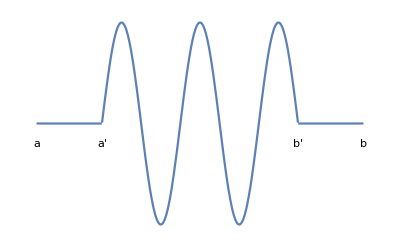

```mathematica
(* FUNCION TEST *)
a = -0.2;
test = Plot[Piecewise[{{0,x<0.2},{0,x>0.8},{Sin[(x-0.2)*(5*Pi/0.6)],x≥0.1 &&x≤0.9}}],{x,0,1}, Axes->False];
labels = {Graphics[Text["a",{0,a}]], Graphics[Text["a'",{0.2,a}]], Graphics[Text["b'",{0.8,a}]], Graphics[Text["b",{1,a}]]};
Show[test,labels]
```

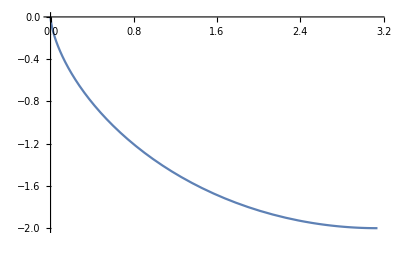

```mathematica
(* CICLOIDE *)
ParametricPlot[{u-Sin[u],Cos[u]-1},{u,0,Pi}]
```

```mathematica
(* ESCALERA DE CANTOR *)
puntos={{-.5,0},{0,0},{1/3,1/2},{2/3,1/2},{1,1},{1.5,1}};
n2 = ListPlot[{{0,0},{1/9,1/4},{2/9,1/4},{1/3,1/2}},PlotJoined->True, PlotStyle->Red,PlotLabel->"n=2"];
n3 = ListPlot[{{2/3,0.5},{1/9+2/3,1/4+0.5},{2/9+2/3,1/4+0.5},{1/3+2/3,1/2+0.5}},PlotJoined->True, PlotStyle->Red];
Show[ListPlot[puntos,PlotJoined->True],ListPlot[{Labeled[{2/3,0.5},"2/3"],Labeled[{1/3,0.5},"1/3"]}],n2,n3]
```

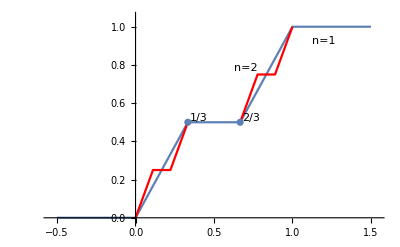
```mathematica
-Graphics-

Show[ListPlot[{{0,0},{1/3,0},{2/3,1},{1,1}},PlotJoined->True],ListPlot[{{1/3,0},{1/3+1/9,1/2},{1/3+2/9,1/2},{2/3,1}},PlotJoined->True, PlotStyle->Red]]
```

-Graphics-

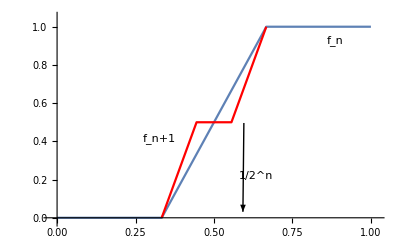

```mathematica
a = 1;  b = -a;
f[x_]:=x*(a*x+b);
Plot[f[x],{x,0,1},AspectRatio->Automatic, Axes->{True,False}, Epilog->{Table[Line[{{i/10,f[i/10]},{i/10,0}}],{i,1,10}]}]
```

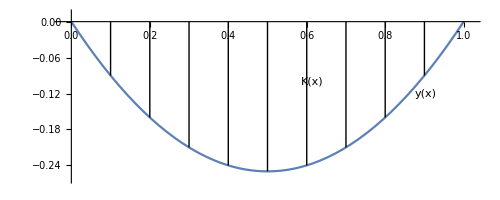

```mathematica
izquierda[x_]:=((x^2)/2)+a*x;
derecha[x_]:=-((x^2)/2)+(x/2)+b*(x-1);
izquierda[0.5] 
derecha[0.5] 
izquierda'[0.5] 
derecha'[0.5]
```

0.125+0.5 a

0.125-0.5 b

0.5+a

0.+b

```mathematica
Solve[{0.125+0.5*x==0.125-0.5*y,0.5+x==y},{x,y}]
```

{{x→-0.25,y→0.25}}

```mathematica
izquierda1[x_]:=((x^2)/2)-0.25*x;
derecha1[x_]:=-((x^2)/2)+(x/2)+0.25*(x-1);
```

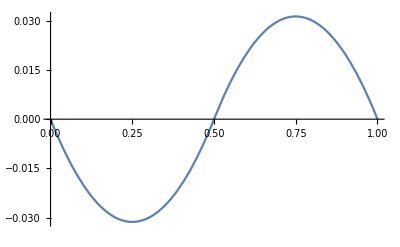

```mathematica
Plot[Piecewise[{{izquierda1[x],x≤0.5},{derecha1[x],x≥0.5}}],{x,0,1}]
```

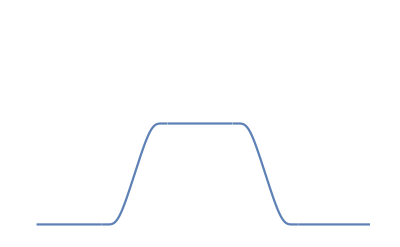

```mathematica
f[x_]:=Piecewise[{ {Exp[-1/x],x>0},{0,x<=0}}];
g[x_]:=f[x]/(f[x]+f[1-x]);
smooth[x_,a_,b_,c_,d_]:=g[(x-a)/(b-a)]*g[(c-x)/(d-c)];
t=1;
Plot[0.5*smooth[x,0,t,t+2,2*t+2],{x,-1,t+4}, PlotRange->{{-1,2*t+2},{0,1}},Axes->False]
```